```mathematica
systemParameters=Import[NotebookDirectory[]<>"systemParameters.csv","CSV"]⟦1⟧;
contours=Import[NotebookDirectory[]<>"contours.csv","CSV"]⟦1⟧;
contourColors=ColorData["PigeonTones"]/@Subdivide[Length@contours];
velocities=Import[NotebookDirectory[]<>"velocity.csv", "CSV"];
specificDrags=Import[NotebookDirectory[]<>"specificDrag.csv", "CSV"];
dataRange={{systemParameters⟦3⟧,systemParameters⟦4⟧},{systemParameters⟦5⟧,systemParameters⟦6⟧}};
```

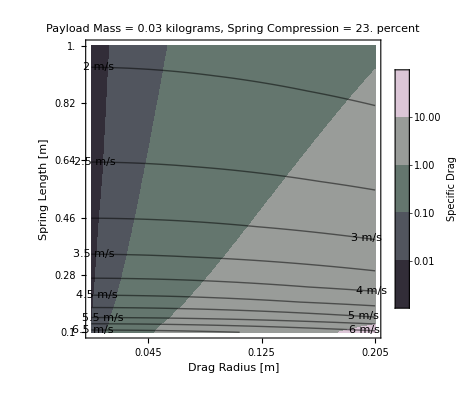

```mathematica
Show[ListContourPlot[specificDrags,PlotRange->All,Contours->contours,ContourStyle->None,DataRange->dataRange,ContourShading->contourColors,PlotLegends->BarLegend[Automatic,LegendLabel->"Specific Drag"],FrameTicks->({#,None}&/@(Subdivide[##,5]&@@@Reverse[dataRange])),FrameLabel->{"Drag Radius [m]","Spring Length [m]"},PlotLabel->"Payload Mass = "<>ToString@Quantity[systemParameters⟦1⟧,"kg"]<>", Spring Compression = "<>ToString@Quantity[100systemParameters⟦2⟧,"Percent"]],ListContourPlot[velocities,(*Contours->Append[Range[5,17,2],{16,Thick}],*)ContourShading->None,ContourLabels->Function[{x,y,z},{Text[Quantity[z,"meters per second"],{x,y},Background->White]}],DataRange->dataRange],ImageSize->Full]
```

```mathematica
Export[NotebookDirectory[]<>DateString[{"Year",".","Month",".","Day",".","Hour24",".","Minute"}]<>"_JumperConfigurationSpace.png",%]
```

/Users/fp/projects/Jumping Robots/2019.07.29.16.41_JumperConfigurationSpace.png

```mathematica
ClearAll[losslessJumpHeight]
losslessJumpHeight[velocity_,gravity_:9.81]:=velocity^2/(2gravity)
```

```mathematica
losslessJumpHeight[5]
```

1.27421